```mathematica
rr14a[n_,m_,d_]:=Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Coth[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}]
rr14[n_,s_,t_]:=rr14a[n,(s+t)/2,(s-t)/2]
```

```mathematica
Expand[rr14[n,s,t]]
```

∑_(j=1)^n j^(1/2 (-s-t)) Cosh[1/2 (s-t) Log[j]]-Coth[ArcTanh[(s-t)/(2 (-1+(s+t)/2))]+1/2 (s-t) Log[n]] ∑_(j=1)^n j^(1/2 (-s-t)) Sinh[1/2 (s-t) Log[j]]

```mathematica
∑_(j=1)^n (1/2 (j^-s+j^-t))-Coth[ArcTanh[(s-t)/(2 (-1+(s+t)/2))]+1/2 (s-t) Log[n]] ∑_(j=1)^n (1/2 (-j^-s+j^-t))
```

FullSimplify[TrigToExp[-Coth[ArcTanh[(s-t)/(2 (-1+(s+t)/2))]+1/2 (s-t) Log[n]]]]

```mathematica
1+2/(-1+(n^(-s+t) (-1+t))/(-1+s))
```

```mathematica
∑_(j=1)^n (1/2 (j^-s+j^-t))+(1+2/(-1+(n^(-s+t) (-1+t))/(-1+s))) ∑_(j=1)^n (1/2 (-j^-s+j^-t))
```

```mathematica
∑_(j=1)^n (1/2 (j^-s+j^-t))+(1+2/(-1+(n^(-s+t) (-1+t))/(-1+s))) ∑_(j=1)^n (1/2 (-j^-s+j^-t))
```

1/2 (1+2/(-1+(n^(-s+t) (-1+t))/(-1+s))) (-HarmonicNumber[n,s]+HarmonicNumber[n,t])+1/2 (HarmonicNumber[n,s]+HarmonicNumber[n,t])

```mathematica
az[n_,s_,t_]:=1/2 (1+2/(-1+(n^(-s+t) (-1+t))/(-1+s))) (-HarmonicNumber[n,s]+HarmonicNumber[n,t])+1/2 (HarmonicNumber[n,s]+HarmonicNumber[n,t])
az2[n_,s_,t_]:=-HarmonicNumber[n,s]/(-1+(n^(-s+t) (-1+t))/(-1+s))+HarmonicNumber[n,t]+HarmonicNumber[n,t]/(-1+(n^(-s+t) (-1+t))/(-1+s))
az3[n_,s_,t_]:=(n^s (-1+s) HarmonicNumber[n,s]-n^t (-1+t) HarmonicNumber[n,t])/(n^s (-1+s)-n^t (-1+t))
ax[n_,s_,t_]:=-HarmonicNumber[n,s]/(-1+(n^(-s+t) (-1+t))/(-1+s))
```

```mathematica
az3[1000000000,.3,.7+I]
```

0.284392-0.841583 ⅈ

```mathematica
Zeta[.7+I]
```

0.284305-0.841353 ⅈ

```mathematica
Expand[1/2 (1+2/(-1+(n^(-s+t) (-1+t))/(-1+s))) (-HarmonicNumber[n,s]+HarmonicNumber[n,t])+1/2 (HarmonicNumber[n,s]+HarmonicNumber[n,t])]
```

-HarmonicNumber[n,s]/(-1+(n^(-s+t) (-1+t))/(-1+s))+HarmonicNumber[n,t]+HarmonicNumber[n,t]/(-1+(n^(-s+t) (-1+t))/(-1+s))

```mathematica
FullSimplify[-HarmonicNumber[n,s]/(-1+(n^(-s+t) (-1+t))/(-1+s))+HarmonicNumber[n,t]+HarmonicNumber[n,t]/(-1+(n^(-s+t) (-1+t))/(-1+s))]
```

(n^s (-1+s) HarmonicNumber[n,s]-n^t (-1+t) HarmonicNumber[n,t])/(n^s (-1+s)-n^t (-1+t))

```mathematica
rr14a[n_,m_,d_]:=Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Coth[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}]
```

```mathematica
FullSimplify[Sum[j^(-d-m)/2+j^(d-m)/2,{j,1,n}]+((1+d-m-(-1+d+m) n^(2 d))/(1+d-m+(-1+d+m) n^(2 d)))Sum[-1/2 j^(-d-m)+j^(d-m)/2,{j,1,n}]]
```

((1+d-m) HarmonicNumber[n,-d+m]+(-1+d+m) n^(2 d) HarmonicNumber[n,d+m])/(1+d-m+(-1+d+m) n^(2 d))

```mathematica
FullSimplify[TrigToExp[-Coth[ArcTanh[d/(-1+m)]+d Log[n]]]]
```

(1+d-m-(-1+d+m) n^(2 d))/(1+d-m+(-1+d+m) n^(2 d))

```mathematica
az2[1000000000000000,N@ZetaZero@1-.5,N@ZetaZero@1]
```

1.36952×10^-8+3.59523×10^-9 ⅈ

```mathematica
Zeta[.7]
```

```mathematica
aza[n_,s_,t_]:=1/2 (1+2/(-1+(n^(-s+t) (-1+t))/(-1+s))) (-HarmonicNumber[n,s])+1/2 (HarmonicNumber[n,s])
```

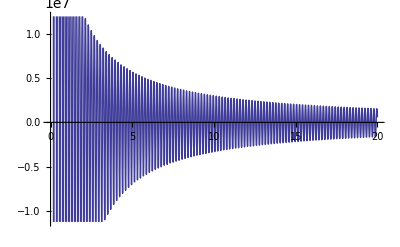

```mathematica
Plot[Re@ aza[1000000000000000,.5,.5+s I ],{s,0,20}]
```

```mathematica
eh[n_,s_]:=Sum[ j^(-1/2) Cos[s Log[n/j]+ArcCot[2s]]/Cos[s Log[n]],{j,1,n}]
eh2[n_,s_]:=Sum[j^(-1/2)  Cos[s Log[n]+ArcCot[2s]],{j,1,n}]
```

```mathematica
eh[100000,60.3518119691]
```

0.534093

```mathematica
Zeta[.5+60.3518119691I]
```

0.538586+1.97639×10^-11 ⅈ

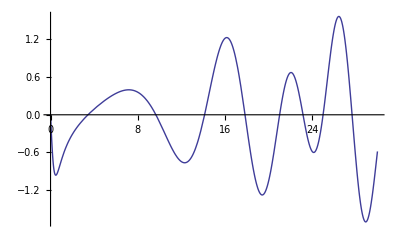

```mathematica
Plot[Im[Zeta[.5+I s]],{s,0,30}]
```

```mathematica
rrx[n_,a_,b_]:=(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]]) HarmonicNumber[n,a+ⅈ b]
rr2[n_,a_,b_]:=2/(1-n^(-2 ⅈ b)((a-1)-ⅈ b)/((a-1)+ⅈ b))HarmonicNumber[n,a+ⅈ b]
rr2z[n_,a_,b_]:=(2n^(I b)((a-1)+ⅈ b))/(n^(I b)((a-1)+ⅈ b)-n^(- ⅈ b)((a-1)-ⅈ b))HarmonicNumber[n,a+ⅈ b]
rr3[n_,s_]:=2(1-n^(Conjugate[s]-s)(Conjugate[s]-1)/(s-1))^-1HarmonicNumber[n,s]
```

```mathematica
rr3[1000000000,.5+60.3518119691I]
```

0.538603+556.17 ⅈ

```mathematica
rr2z[1000000000,.5,60.3518119691]
```

0.538603+556.17 ⅈ

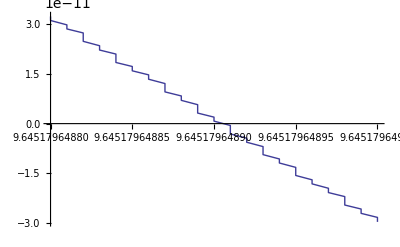

```mathematica
Plot[Im[Zeta[.6+s I]],{s,9.6451796488,9.645179649}]
```

```mathematica
Zeta[.6+9.6451796488I]
```

1.49839+3.22501×10^-11 ⅈ

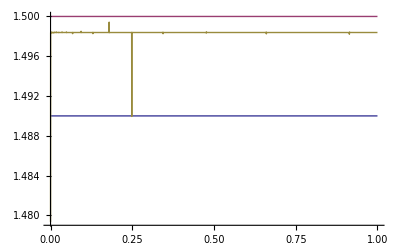

```mathematica
Plot[ {1.49,1.5,Re[ rr3[n,.6+9.6451796488I]]},{n,1,100000000000}]
```

```mathematica
FullSimplify[2/(1-n^(-2 ⅈ b)((a-1)-ⅈ b)/((a-1)+ⅈ b))/.a->1/4]
```

2/(1+((-3 ⅈ+4 b) n^(-2 ⅈ b))/(3 ⅈ+4 b))

```mathematica
Expand[FullSimplify[Expand[(1/2-I b)^2]]]
```

1/4-ⅈ b-b^2

```mathematica
FullSimplify[Expand[(1/2-I b)(1/2+I b)]]
```

1/4+b^2

```mathematica
(2((a-1)+ⅈ b)n^(I b))/(n^(I b)((a-1)+ⅈ b)-n^(- ⅈ b)((a-1)-ⅈ b))
```

(2 (-1+a+ⅈ b) n^(ⅈ b))/(-(-1+a-ⅈ b) n^(-ⅈ b)+(-1+a+ⅈ b) n^(ⅈ b))

```mathematica
FullSimplify[((n^(I b)((a-1)+ⅈ b)-n^(- ⅈ b)((a-1)-ⅈ b) )/(2((a-1)+ⅈ b)n^(I b)))]
```

1/2-((-1+a-ⅈ b) n^(-2 ⅈ b))/(2 (-1+a+ⅈ b))

```mathematica
1/(1/2-((-1+a-ⅈ b) n^(-2 ⅈ b))/(2 (-1+a+ⅈ b)))
```

```mathematica
1/(1/2-((-1+a-ⅈ b) n^(-2 ⅈ b))/(2 (-1+a+ⅈ b)))
```

1/(1/2-((-1/2-ⅈ b) n^(-2 ⅈ b))/(2 (-1/2+ⅈ b)))

```mathematica
N[((-1+a-ⅈ b) n^(-2 ⅈ b))/(2 (-1+a+ⅈ b))//.a->1/2/.b->N@Im@ZetaZero@1]
```

(-0.49875+0.0353297 ⅈ) n^(0.-28.2695 ⅈ)

```mathematica
ExpToTrig[1/(1/2-((-1+a-ⅈ b) n^(-2 ⅈ b))/(2 (-1+a+ⅈ b)))]
```

```mathematica
N[1/(1/2-((-1+a-ⅈ b) n^(-2 ⅈ b))/(2 (-1+a+ⅈ b)))/.a->.5/.b->10/.n->40]
```

1.-0.951135 ⅈ

```mathematica
(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])/.a->.5/.b->10/.n->111114000000
```

1.-0.0809976 ⅈ

```mathematica
rrx[n_,a_,b_]:=(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]]) HarmonicNumber[n,a+ⅈ b]
rrx2[n_,a_,b_]:=(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])Sum[ 1/j^(a+I b),{j,1,n}]
rrx3[n_,a_,b_]:=(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])Sum[ j^-a E^(-I b Log[j]),{j,1,n}]
rrx4[n_,a_,b_]:=(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])Sum[ j^-a (Cos[b Log[j]]-I Sin[ b Log[j]]),{j,1,n}]
rrx5[n_,a_,b_]:=(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])( Sum[ j^-a  Cos[b Log[j]],{j,1,n}]-I Sum[ j^-a  Sin[ b Log[j]],{j,1,n}])
rrx6[n_,a_,b_]:=Sum[ j^-a  Cos[b Log[j]],{j,1,n}]- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]] Sum[ j^-a  Cos[b Log[j]],{j,1,n}]-(  Cot[ArcTan[b/(-1+a)]+b Log[n]])Sum[ j^-a  Sin[ b Log[j]],{j,1,n}]-I Sum[ j^-a  Sin[ b Log[j]],{j,1,n}]
rrx7[n_,a_,b_]:=Sum[ j^-a  (Cos[b Log[j]]-Cot[ArcTan[b/(-1+a)]+b Log[n]]Sin[b Log[j]]),{j,1,n}]-I Sum[ j^-a ( Sin[ b Log[j]]+Cot[ArcTan[b/(-1+a)]+b Log[n]]Cos[b Log[j]]),{j,1,n}]
rrx7a[n_,a_,b_]:=Sum[ j^-a  (Cos[b Log[j]]-Cot[ArcTan[b/(-1+a)]+b Log[n]]Sin[b Log[j]]),{j,1,n}]
rrx7b[n_,a_,b_]:=Sum[ j^-a  (Cos[b Log[j]]+Tan[ArcTan[(1-a)/b]+b Log[n]]Sin[b Log[j]]),{j,1,n}]
```

```mathematica
rrx7b[10000,.5,N@Im@ZetaZero@1+.3]
```

-0.409413

```mathematica
rrx[n,1-a,-b]
```

(1-ⅈ Cot[ArcTan[b/a]-b Log[n]]) HarmonicNumber[n,1-a-ⅈ b]

```mathematica
Zeta[.6+9.6451796488I]
```

1.49839+3.22501×10^-11 ⅈ

```mathematica
rrx7a[100000,.6,9.6451796488]
```

1.49722

```mathematica
Zeta[.6+9.6451796488I]
```

1.49839+3.22501×10^-11 ⅈ

```mathematica
ArcTan[b/(-1+a)]/.a->1/2
```

-ArcTan[2 b]

```mathematica
FullSimplify[j^-a  (Cos[b Log[j]]-Tan[ArcTan[(a-1)/b]-b Log[n]]Sin[b Log[j]])]
```

j^-a (Cos[b Log[j]]+Sin[b Log[j]] Tan[ArcTan[(1-a)/b]+b Log[n]])

```mathematica
Tan[ArcTan[(1-a)/b]]
```

(1-a)/b

```mathematica
rrx7c[n_,a_,b_]:=Sum[ j^-a  ((j^(-ⅈ b)/2+j^(ⅈ b)/2)+((ⅈ (-1+a-ⅈ b+(-1+a+ⅈ b) n^(2 ⅈ b)))/(-1+a-ⅈ b-(-1+a+ⅈ b) n^(2 ⅈ b)))(1/2 ⅈ j^(-ⅈ b)-1/2 ⅈ j^(ⅈ b))),{j,1,n}]
rrx7d[n_,a_,b_]:=Sum[(j^(-a-ⅈ b) ((1-a+ⅈ b) j^(2 ⅈ b)+(-1+a+ⅈ b) n^(2 ⅈ b)))/(1-a+ⅈ b+(-1+a+ⅈ b) n^(2 ⅈ b)),{j,1,n}]
rrx7e[n_,a_,b_]:=((1-a+ⅈ b) HarmonicNumber[n,a-ⅈ b]+(-1+a+ⅈ b) n^(2 ⅈ b) HarmonicNumber[n,a+ⅈ b])/(1-a+ⅈ b+(-1+a+ⅈ b) n^(2 ⅈ b))
```

```mathematica
rrx7e[1000000000,.6,9.6451796488]
```

1.49839-5.66214×10^-14 ⅈ

```mathematica
Zeta[.6+9.6451796488I]
```

1.49839+3.22501×10^-11 ⅈ